# Hopf Normal Form

```mathematica
(-1 + I w)(x + I y) + (x^2+y^2)(x+I y)//Expand
```

-x+ⅈ w x+x^3-ⅈ y-w y+ⅈ x^2 y+x y^2+ⅈ y^3

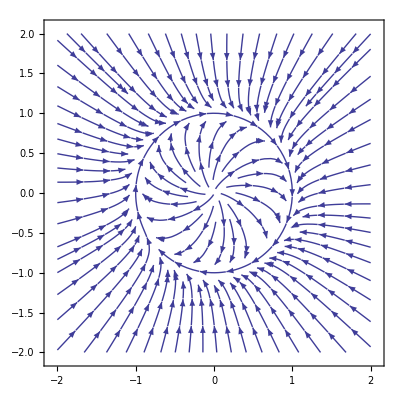

```mathematica
StreamPlot[{x+w y - x(x^2+y^2),-w x+ y - y(x^2+y^2)},{x,-2,2},{y,-2,2}]
```

```mathematica
w = .2;
solution=NDSolve[{x'[t]==x[t] +w y[t] - x[t](x[t]^2+y[t]^2),y'[t]==-w x[t] +y[t] -y[t](x[t]^2+y[t]^2), x[0]==1.001,y[0]==0},{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

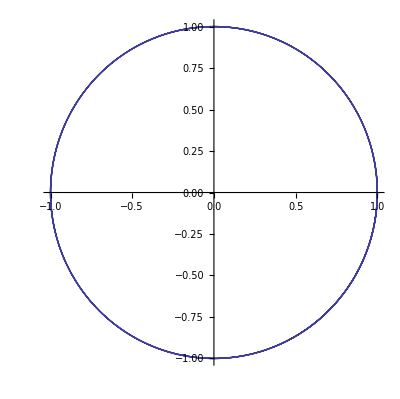

```mathematica
ParametricPlot[{x[t],y[t]}/.solution,{t,0,100}]
```

## Hopf Normal Form

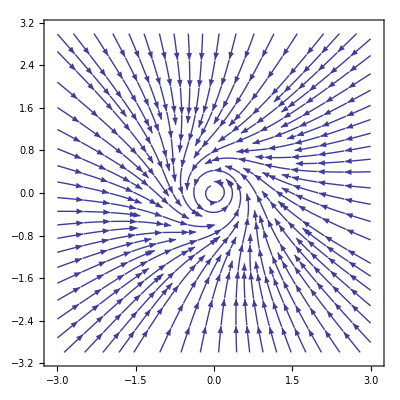

```mathematica
StreamPlot[{.1 x- y -1x(x^2+y^2),x+.1 y - 1y(x^2+y^2)},{x,-3,3},{y,-3,3}]
```

```mathematica
β = 1;
A=1.;
ω=3.6;
```

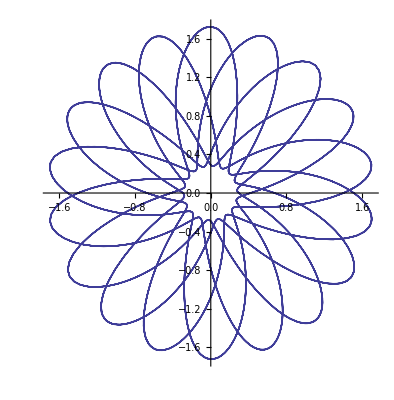

```mathematica
solution=NDSolve[{x'[t]==(β+A ω Sin[ω t]) x[t] - y[t] - x[t](x[t]^2+y[t]^2),y'[t]==x[t] +(β+A ω Sin[ω t]) y[t] -y[t](x[t]^2+y[t]^2), x[0]==60,y[0]==10.0},{x,y},{t,0,1000},MaxSteps->100000];
ParametricPlot[{x[t],y[t]}/.solution,{t,100,100+40Pi},PlotRange->All]
```